Analiza danych z qc

```mathematica
(*path = "/Users/jakub/Developer/qc/qc/files/";*)
path="/media/Developer/qc/qc/files/";
outNames = FileNames["*", path<>"outputs"];
{files, distances} = Transpose@Table[Transpose@Import[outNames[[i]], "TSV"], {i, 1, Length@outNames}];
{length, visibility} = Transpose@ToExpression@Table[StringSplit[FileNameTake[outNames[[i]]], "V"], {i, 1, Length@outNames}];
data =Table[{length[[i]], visibility[[i]], files[[i]], distances[[i]]}, {i, 1, Length@length}];
means = Table[{length[[i]], visibility[[i]], Mean[files[[i]]], Mean[distances[[i]]]},{i,1,Length@length}];
```

```mathematica
ByLength=Gather[means, First[#1]==First[#2]&];
```

```mathematica
Table[Last@Transpose[ByLength[[i]]], {i, 1, Length@ByLength}];
```

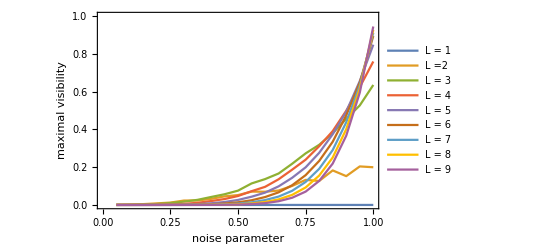

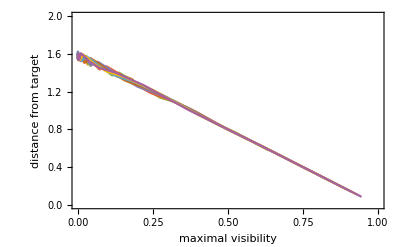

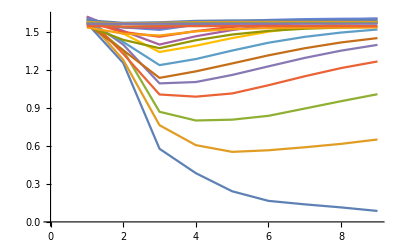

```mathematica
bestT =Table[Transpose[ByLength[[i]]][[3]], {i, 1, Length@ByLength}];
dist=Table[Transpose[ByLength[[i]]][[4]],{i,1,Length@ByLength}];
visibility = Table[Transpose[ByLength[[i]]][[2]], {i, 1, Length@ByLength}];
plotPoints = Table[Transpose@{visibility[[i]], bestT[[i]]}, {i, 1, Length@visibility}];
plots =ListLinePlot[plotPoints, PlotLegends->Placed[{"L = 1", "L =2", "L = 3", "L = 4", "L = 5","L = 6","L = 7","L = 8","L = 9"},{0.6,0.7}], FrameLabel->{"noise parameter", "maximal visibility"},PlotRange->{{0,1},{0,1}}, Frame-> True]
distOfVis=Table[Transpose@{bestT[[i]],dist[[i]]},{i,1,Length@dist}];
plotsDist=ListLinePlot[distPlot,FrameLabel->{"maximal visibility","distance from target"}, PlotRange->{{0,1},{0,2}}, Frame-> True]
distOfLength = Transpose@Table[Transpose@{i, dist[[i]][[v]]}, {i, 1, Length@dist}, {v, -1, - Length[dist[[1]]], -1}];
ListLinePlot@distOfLength
```

```mathematica
Export[path<>"figures/tOFetaplot18-07-2021.png", plots, "PNG", RasterSize-> 2000];
Export[path<>"figures/distOft-21-07-2021.png", plotsDist, "PNG", RasterSize-> 2000];
```

Dopasowanie do prostych (ozn. b - a * d) i porównanie z boundem

```mathematica
distfit = Table[LinearModelFit[distOfVis[[i]], t, t],{i, 1, Length@distOfVis}];
b=Table[distfit[[i]]["BestFitParameters"][[1]],{i,1,Length@distfit}]
a = Table[distfit[[i]]["BestFitParameters"][[2]], {i, 1, Length@distfit}]
```

{1.57957,1.57243,1.57539,1.57658,1.57762,1.57846,1.57908,1.57958,1.58001}

{3.53683×10^11,-1.44331,-1.54169,-1.55037,-1.55805,-1.5625,-1.56481,-1.56599,-1.56716}

Też plot ale już nakładam wiąz k(1-t)

```mathematica
distfit1 = Table[LinearModelFit[distOfVis[[i]], (1-t), t, IncludeConstantBasis->False], {i, 1, Length@distOfVis}];
kvals = Table[distfit1[[i]]["BestFitParameters"], {i, 1, Length@distfit1}];
k = Mean@kvals
```

{1.58068}

```mathematica
Table[plotPoints[[i]][[-2]], {i,1, Length@plotPoints}]
```

{{0.95,3.88365×10^-15},{0.95,0.203991},{0.95,0.526947},{0.95,0.623931},{0.95,0.655876},{0.95,0.647891},{0.95,0.632811},{0.95,0.615901},{0.95,0.594449}}

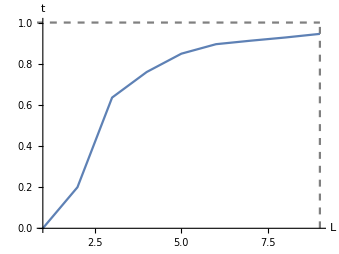

```mathematica
v = -1;
tLpoints = Table[{i, Last[plotPoints[[i]][[v]]]}, {i, 1, Length@plotPoints}];
tL = Show[ParametricPlot[{x,1}, {x,0,9}, PlotStyle->{Gray,Dashed}, PlotRange->{{1,9},{0,1}}],ParametricPlot[{9,y}, {y,0,1}, PlotStyle->{Gray,Dashed}],ListLinePlot[tLpoints, PlotRange->{{1,7},{0,1}}],AxesLabel->{HoldForm[L],HoldForm[t]},PlotLabel->None,LabelStyle->{GrayLevel[0]}, AspectRatio->0.75]
```

```mathematica
Export[path<>"figures/tOfl-18-07-2021.png", tL, "PNG", RasterSize-> 2000];
```